```mathematica
(*Clear["Global`*"];*)
SetDirectory[NotebookDirectory[]];
<<"HeterogeneousTemplate.wl";

GenerateMarkovTemplates[  MarkovProc_, NumTemplates_, LenTemplates_ ] :=
	(RandomFunction[MarkovProc,{#,LenTemplates}][[2]][[1]][[1]])&/@ConstantArray[1,NumTemplates];

RandomMarkovVel[  inputtemplate_,gpo_,EnergyMatrix_,KineticMatrix_ ] :=  Module[ {ErrorProbs, param, kbind, M,gbb, Meff, kpol, ktb,
		coarse, Probs, temp, copysize, templatesize, ProbsUnnormed, AllOutput,
		visitationMatrixls,Lengthtimes,Ggen},
	copysize = 2;
	templatesize = 2;
	
	param =SmallkbindPermanent[gpo,copysize,templatesize,12];
	
	kbind = param[[1]];
	M = param[[2]]; 
	gbb= param[[3]];
	kpol = param[[4]];
	
	coarse = GetProbabilityTensor[gpo,EnergyMatrix,KineticMatrix,
		copysize,templatesize,kbind,M];
	
	Probs = GetProbabilityTensorFine[gbb,EnergyMatrix,kbind,
		kpol,M,copysize,templatesize];
	
	temp = GetKineticTensors[gbb,EnergyMatrix,kbind,kpol,M,copysize,templatesize];
	
	ProbsUnnormed = GetUnnormedProbabilityTensor[gbb,EnergyMatrix,
		kbind,kpol,M,copysize,templatesize];
		
	AllOutput = GetTransferMatrixList[gpo,EnergyMatrix,KineticMatrix,
			inputtemplate,kbind,M];
	
	visitationMatrixls = GetVisitationList[AllOutput[[2]]][[1]];
				
	Lengthtimes =GetTimes[ visitationMatrixls, gpo,temp,copysize,
			templatesize,inputtemplate][[2]];
	
	Return[Length[inputtemplate]/Total[Lengthtimes]];
	
 ]

(*No ktb or Meff or Ggen required*)
SmallkbindPermanent[gpo_,copysize_,templatesize_,kineticFactor_] :=
	(*kbind, M, gbb, kpol*)
	{ConstantArray[1,{copysize, templatesize}],Exp[-kineticFactor]*ConstantArray[1,copysize],gpo+kineticFactor,
	Exp[kineticFactor]*ConstantArray[1,{copysize,templatesize,copysize,templatesize}]}
```

{{2.,0},{0,2.}}

{{2.,0},{0,4.}}

{{2.,0},{0,6.}}

{{2.,0},{0,8.}}

{{2.,0},{0,10.}}

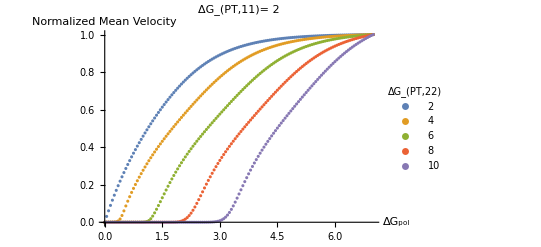

```mathematica
copysize= 2;
templatesize = 2;
Get["masterTemplate"];
inputtemplate = masterTemplate;
KineticMatrix = {{0.0,0.0},{0.0,0.0}};
velData = {};
Raw = {};

For [ x = 2.0,x<10.1,x = x+2.0,
	BaseEnergyMatrix =  {{2.0,0},{0,x}};
	Print[BaseEnergyMatrix];
	(*EnergyMatrix Takes into account corrections due to bases being placed after correct or incorrect pairs*)
		EnergyMatrix = ConstantArray[0.0,{2,2,2,2}];
		For [i = 1, i<= 2, i++,
			For [d = 1, d<= 2, d++,
				For [j = 1, j<= 2, j++,
					EnergyMatrix[[i]][[d]][[j]][[j]] = BaseEnergyMatrix[[j]][[j]];
				]
			]		
		];
	Fmin = -Log[PartitionFunc[Exp[EnergyMatrix],Exp[EnergyMatrix[[1]][[2]][[;;]][[1]]],Exp[EnergyMatrix[[1]][[2]][[;;]][[2]]],inputtemplate]]/Length[inputtemplate];	
	Domain = Range[Fmin,Fmin+7.0,0.05];
	PlotDomain = Domain-Fmin;
	MeanVel =RandomMarkovVel[  inputtemplate,#,EnergyMatrix,KineticMatrix] &/@ Domain;
	velNorm = MeanVel/Last[MeanVel];
	velData =Append[velData,Transpose@{PlotDomain,velNorm}];
	Raw =Append[Raw,Transpose@{PlotDomain,MeanVel}];
]

mu={2,4,6,8,10};
pl=PointLegend[mu,LegendLabel->Subscript["ΔG","PT,22"],LegendFunction->"Frame",LegendLayout->Automatic,LegendMarkers->Automatic];
p1 =ListPlot[velData,AxesLabel->{Subscript["ΔG","pol"],"Normalized Mean Velocity"},
		PlotLegends->Placed[pl,Right],PlotLabel->Row[{Subscript["ΔG","PT,11"],"= 2"}]]
```

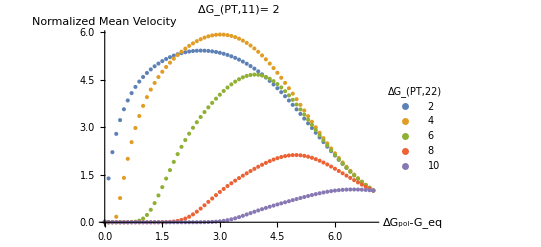

```mathematica
mu={2,4,6,8,10};
pl=PointLegend[mu,LegendLabel->Subscript["ΔG","PT,22"],LegendFunction->"Frame",LegendLayout->Automatic,LegendMarkers->Automatic];
p1 =ListPlot[velData,AxesLabel->{Row[{Subscript["ΔG","pol"],"-",Subscript["G","eq"]}],"Normalized Mean Velocity"},
		PlotLegends->Placed[pl,Right],PlotLabel->Row[{Subscript["ΔG","PT,11"],"= 2"}]]
```

```mathematica
Save["PermTherm.NormalizedVelocityData",velData]
Save["PermTherm.RawVelocityData",Raw]
```

-5.533773810444821717145571938967888892217799936889207292766873892220477210140737598730922082404670422321068

{-5.6,-5.533773810444821717145571938967888892217799936889207292766873892220477210140737598730922082404670422321068,-5.4,-5.2,-5.,-4.8,-4.6,-4.4,-4.2,-4.,-3.8,-3.6,-3.4,-3.2,-3.,-2.8,-2.6,-2.4,-2.2,-2.,-1.8,-1.6,-1.4,-1.2,-1.,-0.8,-0.6,-0.4,-0.2,0.,0.2,0.4,0.6,0.8,1.}

```mathematica
Ceiling[Fmin,0.5]
```

-2.

```mathematica
EnergyMatrix[[All,All,2,2]]
```

{{10.,10.},{10.,10.}}

```mathematica
Length[inputtemplate[[10,9]]]
```

100

{2,2,2,1,2,1,1,1,1,2,1,2,1,1,1,2,1,1,1,2,2,2,2,1,1,2,1,2,2,1,1,1,2,1,2,1,1,1,1,2,2,1,2,2,1,2,2,2,2,2,1,1,2,1,2,1,2,2,2,2,2,2,2,2,2,1,2,1,2,2,2,2,1,2,2,2,2,1,1,2,1,1,2,1,1,1,2,2,1,2,2,1,2,1,2,1,2,2,1,1,1,2,1,1,2,2,1,2,1,1,2,1,1,2,1,2,1,1,2,1,1,1,2,2,2,2,2,1,1,1,1,1,1,1,2,2,1,2,1,2,2,2,1,1,1,1,2,2,1,2,1,1,2,2,2,1,2,1,2,1,2,1,2,1,1,2,1,1,2,2,1,1,2,1,2,1,1,1,2,1,1,1,2,1,1,1,1,2,1,2,1,1,1,1,2,2,1,2,2,2,1,2,2,1,1,2,1,2,1,1,2,1,2,2,1,2,1,1,1,2,1,1,1,1,2,2,1,1,2,1,2,2,1,2,2,1,2,2,2,2,2,1,2,2,2,2,2,1,1,2,2,2,1,2,1,2,2,1,2,2,1,2,1,2,2,1,2,1,2,1,1,1,1,1,2,1,1,1,1,1,1,2,2,2,2,1,2,1,2,1,1,2,1,1,1,1,1,2,1,2,2,1,2,2,2,2,2,1,2,2,2,2,1,1,1,1,2,1,2,2,2,2,1,2,1,2,2,2,2,2,2,1,1,1,1,1,2,2,2,1,2,1,2,2,1,1,1,1,2,1,1,2,2,2,1,1,2,1,2,2,2,2,1,1,2,1,2,1,2,1,2,1,1,2,2,2,2,2,1,1,2,2,2,2,2,2,2,2,1,2,1,2,2,2,2,1,1,1,1,1,2,2,2,2,1,1,1,1,1,1,2,1,2,2,2,2,1,2,1,1,1,1,2,2,2,2,2,1,2,1,1,2,2,1,2,2,1,2,2,2,1,2,1,1,1,1,2,2,1,1,2,1,1,1,1,2,1,1,1,2,2,1,2,1,2,2,2,2,2,2,2,2,1,1,1,1,2,1,2,1,1,1,2,2,1,2,1,1,2,2,1,1,2,2,1,2,2,2,2,1,1,2,2,1,2,1,1,2,2,2,1,1,1,2,1,2,1,2,2,1,2,2,2,2,1,1,1,1,1,1,2,1,1,1,1,2,2,2,2,1,1,1,1,2,2,1,2,2,1,2,1,1,2,1,1,1,1,2,1,1,1,1,1,2,2,1,1,2,2,1,1,1,2,2,2,1,2,2,2,1,1,2,1,2,2,1,2,1,1,1,1,1,2,1,1,1,1,2,1,2,2,2,2,2,2,1,2,2,1,1,2,2,2,2,1,2,2,2,2,2,2,2,2,2,1,2,2,2,2,1,2,1,2,1,1,2,1,1,1,2,1,2,1,2,2,2,2,1,2,2,1,1,2,2,1,1,1,1,1,2,1,2,2,2,2,1,1,1,1,2,1,1,1,2,2,2,1,2,2,2,2,1,2,2,1,1,1,1,1,2,2,2,2,2,2,1,1,2,2,2,2,1,2,1,1,2,1,2,1,2,2,1,2,2,2,1,1,2,1,2,2,2,1,2,1,1,2,1,2,1,2,2,1,1,2,2,1,1,2,2,2,2,2,2,2,2,2,1,1,1,2,2,1,1,1,1,2,1,1,2,2,1,1,1,2,1,1,2,1,2,2,1,2,2,2,2,2,2,1,2,1,1,2,2,1,2,2,1,2,1,2,2,2,2,1,2,2,1,1,2,2,1,1,2,1,1,2,1,2,2,2,1,2,2,2,2,1,2,1,2,2,2,1,1,2,1,1,1,2,1,2,1,1,1,1,2,2,2,1,2,1,1,1,2,1,2,1,1,2,1,1,2,2,1,1,1,2,1,1,1,1,1,2,2,2,2,1,1,1,1,2,2,2,2,1,1,1,1,2,2,1,1,1,1,2,2,1,1,1,1,1,2,2,1,1,1,2,1,1,2,1,1,2,2,1,1,1,1,1,2,1,1,1,2,2,1,1,1,1,1,1,2,1,2,1,1,2,2,1,1,2,2,2,2,1,1,2,2,1,1,2,2,1,2,2,1,1,1,1,2,1,2,2,1,2,2,2,2,1,2,2,1,1,1,2,2,1,2,2,1,2,2,1,1,2,2,1,2,1,2,1,2,2,1,1,2,2,2,1,1,2,1,1,1,2,1,2,1,2,2}

```mathematica
Clear[masterTemplate]
```

```mathematica
masterTemplate
```

{2,2,2,1,2,1,1,1,1,2,1,2,1,1,1,2,1,1,1,2,2,2,2,1,1,2,1,2,2,1,1,1,2,1,2,1,1,1,1,2,2,1,2,2,1,2,2,2,2,2,1,1,2,1,2,1,2,2,2,2,2,2,2,2,2,1,2,1,2,2,2,2,1,2,2,2,2,1,1,2,1,1,2,1,1,1,2,2,1,2,2,1,2,1,2,1,2,2,1,1,1,2,1,1,2,2,1,2,1,1,2,1,1,2,1,2,1,1,2,1,1,1,2,2,2,2,2,1,1,1,1,1,1,1,2,2,1,2,1,2,2,2,1,1,1,1,2,2,1,2,1,1,2,2,2,1,2,1,2,1,2,1,2,1,1,2,1,1,2,2,1,1,2,1,2,1,1,1,2,1,1,1,2,1,1,1,1,2,1,2,1,1,1,1,2,2,1,2,2,2,1,2,2,1,1,2,1,2,1,1,2,1,2,2,1,2,1,1,1,2,1,1,1,1,2,2,1,1,2,1,2,2,1,2,2,1,2,2,2,2,2,1,2,2,2,2,2,1,1,2,2,2,1,2,1,2,2,1,2,2,1,2,1,2,2,1,2,1,2,1,1,1,1,1,2,1,1,1,1,1,1,2,2,2,2,1,2,1,2,1,1,2,1,1,1,1,1,2,1,2,2,1,2,2,2,2,2,1,2,2,2,2,1,1,1,1,2,1,2,2,2,2,1,2,1,2,2,2,2,2,2,1,1,1,1,1,2,2,2,1,2,1,2,2,1,1,1,1,2,1,1,2,2,2,1,1,2,1,2,2,2,2,1,1,2,1,2,1,2,1,2,1,1,2,2,2,2,2,1,1,2,2,2,2,2,2,2,2,1,2,1,2,2,2,2,1,1,1,1,1,2,2,2,2,1,1,1,1,1,1,2,1,2,2,2,2,1,2,1,1,1,1,2,2,2,2,2,1,2,1,1,2,2,1,2,2,1,2,2,2,1,2,1,1,1,1,2,2,1,1,2,1,1,1,1,2,1,1,1,2,2,1,2,1,2,2,2,2,2,2,2,2,1,1,1,1,2,1,2,1,1,1,2,2,1,2,1,1,2,2,1,1,2,2,1,2,2,2,2,1,1,2,2,1,2,1,1,2,2,2,1,1,1,2,1,2,1,2,2,1,2,2,2,2,1,1,1,1,1,1,2,1,1,1,1,2,2,2,2,1,1,1,1,2,2,1,2,2,1,2,1,1,2,1,1,1,1,2,1,1,1,1,1,2,2,1,1,2,2,1,1,1,2,2,2,1,2,2,2,1,1,2,1,2,2,1,2,1,1,1,1,1,2,1,1,1,1,2,1,2,2,2,2,2,2,1,2,2,1,1,2,2,2,2,1,2,2,2,2,2,2,2,2,2,1,2,2,2,2,1,2,1,2,1,1,2,1,1,1,2,1,2,1,2,2,2,2,1,2,2,1,1,2,2,1,1,1,1,1,2,1,2,2,2,2,1,1,1,1,2,1,1,1,2,2,2,1,2,2,2,2,1,2,2,1,1,1,1,1,2,2,2,2,2,2,1,1,2,2,2,2,1,2,1,1,2,1,2,1,2,2,1,2,2,2,1,1,2,1,2,2,2,1,2,1,1,2,1,2,1,2,2,1,1,2,2,1,1,2,2,2,2,2,2,2,2,2,1,1,1,2,2,1,1,1,1,2,1,1,2,2,1,1,1,2,1,1,2,1,2,2,1,2,2,2,2,2,2,1,2,1,1,2,2,1,2,2,1,2,1,2,2,2,2,1,2,2,1,1,2,2,1,1,2,1,1,2,1,2,2,2,1,2,2,2,2,1,2,1,2,2,2,1,1,2,1,1,1,2,1,2,1,1,1,1,2,2,2,1,2,1,1,1,2,1,2,1,1,2,1,1,2,2,1,1,1,2,1,1,1,1,1,2,2,2,2,1,1,1,1,2,2,2,2,1,1,1,1,2,2,1,1,1,1,2,2,1,1,1,1,1,2,2,1,1,1,2,1,1,2,1,1,2,2,1,1,1,1,1,2,1,1,1,2,2,1,1,1,1,1,1,2,1,2,1,1,2,2,1,1,2,2,2,2,1,1,2,2,1,1,2,2,1,2,2,1,1,1,1,2,1,2,2,1,2,2,2,2,1,2,2,1,1,1,2,2,1,2,2,1,2,2,1,1,2,2,1,2,1,2,1,2,2,1,1,2,2,2,1,1,2,1,1,1,2,1,2,1,2,2}